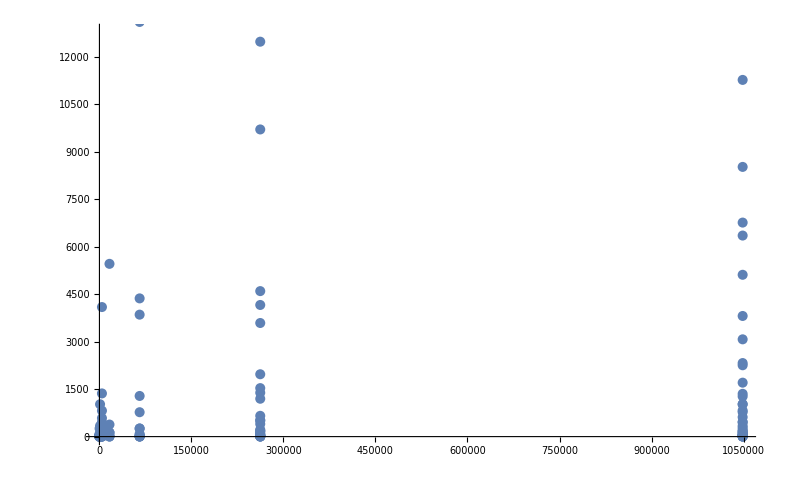

```mathematica
ListPlot[Flatten[Table[Map[{k,#}&,Divisors[k]],{k,Table[4^n-1,{n,1,10}]}],1]]
```

```mathematica
erdos=Table[10^n-1,{n,1,100}];
```

```mathematica
Select[With[{j=5},Table[If[Mod[erdos[[i]],erdos[[j]]]==0,{i,j},Null],{i,Length[erdos]}]],ToString[#]≠ToString[Null]&]
```

{{5,5},{10,5}}

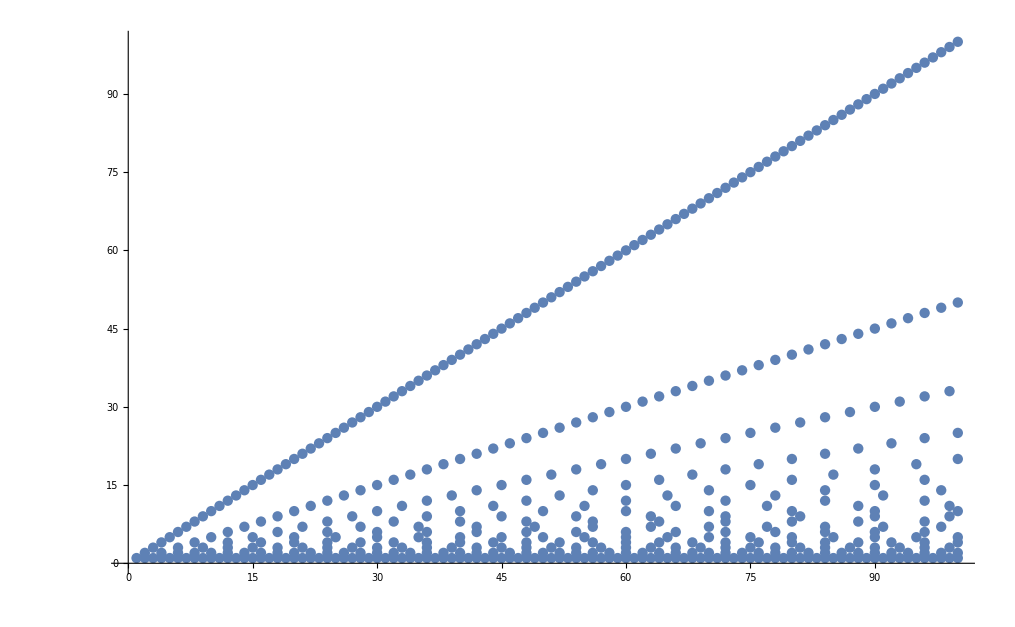

```mathematica
ListPlot[Select[Flatten[Table[If[Mod[erdos[[i]],erdos[[j]]]==0,{i,j},Null],{i,Length[erdos]},{j,Length[erdos]}],1],ToString[#]≠ToString[Null]&]]
```

```mathematica
Table[Map[{n,#}&,Divisors[n]],{n,1,100}]
```

```mathematica
ListPlot[Flatten[Table[Map[{n,#}&,Divisors[n]],{n,1,100000}],1]]
```

$Aborted

```mathematica
Simplify[Sort[Flatten[Table[Map[{n,#}&,Divisors[n]],{n,1,1000}],1]]==Sort[Select[Flatten[Table[If[Mod[erdos[[i]],erdos[[j]]]==0,{i,j},Null],{i,Length[erdos]},{j,Length[erdos]}],1],ToString[#]≠ToString[Null]&]]]
```

True

```mathematica
Table[Map[{k,#}&,Divisors[k]],{k,Table[4^n-1,{n,1,10}]}]
```

{{{3,1},{3,3}},{{15,1},{15,3},{15,5},{15,15}},{{63,1},{63,3},{63,7},{63,9},{63,21},{63,63}},{{255,1},{255,3},{255,5},{255,15},{255,17},{255,51},{255,85},{255,255}},{{1023,1},{1023,3},{1023,11},{1023,31},{1023,33},{1023,93},{1023,341},{1023,1023}},{{4095,1},{4095,3},{4095,5},{4095,7},{4095,9},{4095,13},{4095,15},{4095,21},{4095,35},{4095,39},{4095,45},{4095,63},{4095,65},{4095,91},{4095,105},{4095,117},{4095,195},{4095,273},{4095,315},{4095,455},{4095,585},{4095,819},{4095,1365},{4095,4095}},{{16383,1},{16383,3},{16383,43},{16383,127},{16383,129},{16383,381},{16383,5461},{16383,16383}},{{65535,1},{65535,3},{65535,5},{65535,15},{65535,17},{65535,51},{65535,85},{65535,255},{65535,257},{65535,771},{65535,1285},{65535,3855},{65535,4369},{65535,13107},{65535,21845},{65535,65535}},{{262143,1},{262143,3},{262143,7},{262143,9},{262143,19},{262143,21},{262143,27},{262143,57},{262143,63},{262143,73},{262143,133},{262143,171},{262143,189},{262143,219},{262143,399},{262143,511},{262143,513},{262143,657},{262143,1197},{262143,1387},{262143,1533},{262143,1971},{262143,3591},{262143,4161},{262143,4599},{262143,9709},{262143,12483},{262143,13797},{262143,29127},{262143,37449},{262143,87381},{262143,262143}},{{1048575,1},{1048575,3},{1048575,5},{1048575,11},{1048575,15},{1048575,25},{1048575,31},{1048575,33},{1048575,41},{1048575,55},{1048575,75},{1048575,93},{1048575,123},{1048575,155},{1048575,165},{1048575,205},{1048575,275},{1048575,341},{1048575,451},{1048575,465},{1048575,615},{1048575,775},{1048575,825},{1048575,1023},{1048575,1025},{1048575,1271},{1048575,1353},{1048575,1705},{1048575,2255},{1048575,2325},{1048575,3075},{1048575,3813},{1048575,5115},{1048575,6355},{1048575,6765},{1048575,8525},{1048575,11275},{1048575,13981},{1048575,19065},{1048575,25575},{1048575,31775},{1048575,33825},{1048575,41943},{1048575,69905},{1048575,95325},{1048575,209715},{1048575,349525},{1048575,1048575}}}